## Entries s_{ij} with i, j<4

```mathematica
Integrate[Exp[-u/z-u ζ],{ζ,0,1}]/Exp[-u/z-u ]-1//FullSimplify
```

(-1+ⅇ^u-u)/u

```mathematica
Integrate[Exp[-u z ζ-u],{ζ,0,1}]/Exp[-u z-u ]-1//FullSimplify
```

(-1+ⅇ^(u z)-u z)/(u z)

```mathematica
Integrate[Exp[-u/z-u ζ](u/z+u ζ),{ζ,0,1}]/Exp[-u/z-u ]-(u/z+u)//FullSimplify
```

-(z+u (1+u) (1+z)-ⅇ^u (u+z))/(u z)

```mathematica
Integrate[Exp[-u z ζ-u](u z ζ+u),{ζ,0,1}]/Exp[-u z-u ]-(u z+u)//FullSimplify
```

(-1+ⅇ^(u z) (1+u)-u (1+z) (1+u z))/(u z)

```mathematica
Integrate[Exp[-u/z-u ζ](ζ^2u^2/z),{ζ,0,1}]-Exp[-u/z-u ](u^2/z)//FullSimplify
```

-(ⅇ^(-(u (1+z))/z) (-2 ⅇ^u+(1+u) (2+u^2)))/(u z)

```mathematica
Integrate[Exp[-u z ζ-u](ζ^2u^2 z),{ζ,0,1}]-Exp[-u z-u ](u^2 z)//FullSimplify
```

(ⅇ^(-u (1+z)) (2 ⅇ^(u z)-(1+u z) (2+u^2 z^2)))/(u z^2)

## Entry s_{33}

```mathematica
Integrate[Integrate[(((Exp[u]-1)/u-1)Exp[-u-u/z]+((Exp[u z]-1)/(u z)-1)Exp[-u-u z])/(u z),{u,0,Infinity},Assumptions->0<z<1],{z,0,1}]
```

-2+Log[16]

```mathematica
Integrate[((Exp[u](u+z)-u(u+1)(z+1)-z)Exp[-u-u/z]/(u z)+(Exp[u z](u+1)-u(z+1)(u z+1)-1)Exp[-u-u z]/(u z))/(u z),{u,0,Infinity},Assumptions->0<z<1]
```

0

```mathematica
Integrate[Integrate[(-(ⅇ^(-(u (1+z))/z) (-2 ⅇ^u+(1+u) (2+u^2)))/(u z)+(ⅇ^(-u (1+z)) (2 ⅇ^(u z)-(1+u z) (2+u^2 z^2)))/(u z^2))/(u z),{u,0,Infinity},Assumptions->0<z<1],{z,0,1}]
```

-2+Log[4]

```mathematica
Integrate[((Exp[u](u-2)+u+2)Exp[-u-u/z]/(u z)+(Exp[u z](u z-2)+u z+2)Exp[-u-u z]/(u z^2))/(u z),{u,0,Infinity},Assumptions->0<z<1]
```

(-4 z+2 (2+z) Log[1+z])/z^3

```mathematica
s33[w_,p_]:=Log[16]-2+p[0]^2(-2+Log[4])+p[0]*NIntegrate[(-4 z+2 (2+z) Log[1+z])/z^3 p[z],{z,0,1}]
```

```mathematica
ρ0[z_]:=1-z
```

```mathematica
s33[1,ρ0]//FullSimplify
```

0.286538

## Entry s_{32}

```mathematica
Integrate[Integrate[(((Exp[u]-1)/u-1)Exp[-u-u/z](u/z)^w+((Exp[u z]-1)/(u z)-1)Exp[-u-u z](u z)^w)/(u z),{u,0,Infinity},Assumptions->0<z<1&&0<w<1],{z,0,1},Assumptions->0<w<1]
```

(2^-w Gamma[-1+w] (-4+2 w+2^w (3+(-3+w) w)-2 (-1+w) Hypergeometric2F1[1,1,1+w,-1]))/(-1+w)

```mathematica
Integrate[Integrate[((Exp[u](u+z)-u(u+1)(z+1)-z)Exp[-u-u/z]/(u z)(u/z)^w+(Exp[u z](u+1)-u(z+1)(u z+1)-1)Exp[-u-u z]/(u z)(u z)^w)/(u z),{u,0,Infinity},Assumptions->0<z<1&&0<w<1],{z,0,1},Assumptions->0<w<1]
```

(2^-w Gamma[1+w] (-4+2 w+2^w (3+(-3+w) w)-2 (-1+w) Hypergeometric2F1[1,1,1+w,-1]))/(-1+w)^2

```mathematica
Integrate[Expand[Integrate[(-(ⅇ^(-(u (1+z))/z) (-2 ⅇ^u+(1+u) (2+u^2)))/(u z)(u/z)^w+(ⅇ^(-u (1+z)) (2 ⅇ^(u z)-(1+u z) (2+u^2 z^2)))/(u z^2)(u z)^w)/(u z),{u,0,Infinity},Assumptions->0<z<1&&0<w<1]],{z,0,1},Assumptions->0<w<1]
```

(2^(-1-w) (-4 (2+w)+2^w (8-w (4+(-3+w) w))) Gamma[-1+w])/(-2+w)

```mathematica
Integrate[((Exp[u](u-2)+u+2)Exp[-u-u/z]/(u z)*(u/z)^w+(Exp[u z](u z-2)+u z+2)Exp[-u-u z]/(u z^2)*(u z)^w)/(u z),{u,0,Infinity},Assumptions->0<z<1&&0<w<1]
```

((1+z)^-w (1+z^w) (2+z+w z+(1+z)^w (-2+(-1+w) z)) Gamma[-1+w])/z^3

```mathematica
s32[w_,p_]:=-w*(1/(-1+w)2^-w Gamma[-1+w] (-4+2 w+2^w (3+(-3+w) w)-2 (-1+w) Hypergeometric2F1[1,1,1+w,-1])+1/(-1+w)^2 2^-w Gamma[1+w] (-4+2 w+2^w (3+(-3+w) w)-2 (-1+w) Hypergeometric2F1[1,1,1+w,-1])p[0]+1/(-2+w)2^(-1-w) (-4 (2+w)+2^w (8-w (4+(-3+w) w))) Gamma[-1+w]p[0]^2+p[0]*NIntegrate[1/z^3(1+z)^-w (1+z^w) (2+z+w z+(1+z)^w (-2+(-1+w) z)) Gamma[-1+w]p[z],{z,0,1}])
```

```mathematica
s23[w_,p_]:=s32[w,p]
```

```mathematica
s32[.9999,ρiid]
```

-0.437764

## Entry s_{31}, V2

```mathematica
eps=10^-5
```

1/100000

```mathematica
helpr[p_,w_]:=NIntegrate[1/z^3(1+z)^-w (1+z^w) (2+z+w z+(1+z)^w (-2+(-1+w) z)) Gamma[-1+w]p[z],{z,10^-4,1},AccuracyGoal->5]
```

```mathematica
s31[ww_,p_]:=s32[ww,p]*(-1/w)+D[1/(-1+w)2^-w Gamma[-1+w] (-4+2 w+2^w (3+(-3+w) w)-2 (-1+w) Hypergeometric2F1[1,1,1+w,-1])+1/(-1+w)^2 2^-w Gamma[1+w] (-4+2 w+2^w (3+(-3+w) w)-2 (-1+w) Hypergeometric2F1[1,1,1+w,-1])p[0]+1/(-2+w)2^(-1-w) (-4 (2+w)+2^w (8-w (4+(-3+w) w))) Gamma[-1+w]p[0]^2,w]+p[0]*(helpr[p,ww]-helpr[p,ww-eps])/eps(*NIntegrate[D[1/z^3(1+z)^-q (1+z^q) (2+z+q z+(1+z)^q (-2+(-1+q) z)) Gamma[-1+q],q]p[z]/.{q->ww},{z,10^-10,1}]*)/.{w->ww}
```

```mathematica
s13[w_,p_]:=s31[w,p]
```

```mathematica
ρiid[z_]:=1-z
```

```mathematica
s31[.99,Function [x,ρkink[x,.94]]]
```

0.723449

```mathematica
N[4-7/2Zeta[3]+7/2Log[2]^2-9Log[2]+7Pi^2/12-EulerGamma(Pi^2/3+2-7Log[2])]
```

0.740604

## Entry s_{22}

```mathematica
T221[w_]=Integrate[Integrate[(((Exp[u]-1)/u-1)Exp[-u-u/z](u/z)^w+((Exp[u z]-1)/(u z)-1)Exp[-u-u z](u z)^w)/(u^(1-w) z),{u,0,Infinity},Assumptions->0<z<1&&0<w<1],{z,0,1},Assumptions->0<w<1]
```

-(2 Gamma[-1+2 w] (-1+Hypergeometric2F1[-1+w,2 w,w,-1]+2 (-1+w) Hypergeometric2F1[w,2 w,1+w,-1]))/(-1+w)

```mathematica
T222[w_]=Integrate[Integrate[((Exp[u](u+z)-u(u+1)(z+1)-z)Exp[-u-u/z]/(u z)(u/z)^w+(Exp[u z](u+1)-u(z+1)(u z+1)-1)Exp[-u-u z]/(u z)(u z)^w)/(u^(1-w) z),{u,0,Infinity},Assumptions->0<z<1&&0<w<1],{z,0,1},Assumptions->0<w<1]
```

(4 Gamma[1+w]^2)/(1-2 w)-8 w Gamma[-2+2 w] (-1+Hypergeometric2F1[-1+w,2 w,w,-1])

```mathematica
T223[w_]=Integrate[Expand[Integrate[(-(ⅇ^(-(u (1+z))/z) (-2 ⅇ^u+(1+u) (2+u^2)))/(u z)(u/z)^w+(ⅇ^(-u (1+z)) (2 ⅇ^(u z)-(1+u z) (2+u^2 z^2)))/(u z^2)(u z)^w)/(u^(1-w) z),{u,0,Infinity},Assumptions->0<z<1&&1/2<w<1]],{z,0,1},Assumptions->1/2<w<1]
```

(4^-w (2 (1+w) (4 (-1+4^w)+w (2 (-3+4^w)+w (-9+2 w (-5+4 w)))) Gamma[-1+2 w]-(-1+w) w Gamma[2+2 w] Hypergeometric2F1[1,-2-w,w,-1]))/((-2+w) (1+w) (2+w))

```mathematica
Integrate[((Exp[u](u-2)+u+2)Exp[-u-u/z]/(u z)*(u/z)^w+(Exp[u z](u z-2)+u z+2)Exp[-u-u z]/(u z^2)*(u z)^w)/(u^(1-w) z),{u,0,Infinity},Assumptions->0<z<1&&0<w<1]
```

2 z^(-3+w) (1+z)^(-2 w) (2+z+2 w z+(1+z)^(2 w) (-2+(-1+2 w) z)) Gamma[-1+2 w]

```mathematica
s22[w_,p_]:=w^2*(T221[w]+T222[w]p[0]+T223[w]p[0]^2+p[0]*NIntegrate[2 z^(-3+w) (1+z)^(-2 w) (2+z+2 w z+(1+z)^(2 w) (-2+(-1+2 w) z)) Gamma[-1+2 w] p[z],{z,0,1}])
```

```mathematica
s22[.99999,ρiid]
```

0.817736

```mathematica
N[12 Log[2]-15/2]
```

0.817766

## Entry s_21

#### independent of rho

```mathematica
Integrate[(((Exp[u]-1)/u-1)Exp[-u-u/z](u/z)^t+((Exp[u z]-1)/(u z)-1)Exp[-u-u z](u z)^t)/(u^(1-w) z),{u,0,Infinity},Assumptions->0<z<1&&1/2<w<1&&1/2<t<1]
```

((1+z)^(-t-w) (z^t+z^w) (-1-(t+w) z+(1+z)^(t+w)) Gamma[-1+t+w])/z^2

```mathematica
(*frakT[w_,t_]:=*)Integrate[1/z^2(1+z)^(-t-w) (z^t+z^w) (-1-(t+w) z+(1+z)^(t+w)) Gamma[-1+t+w],{z,0,1},Assumptions->1/2<w<1&&1/2<t<1]
```

Gamma[-1+t+w] (1/(-1+t)+1/(-1+w)-Hypergeometric2F1[-1+t,t+w,t,-1]/(-1+t)-((t+w) Hypergeometric2F1[t,t+w,1+t,-1])/t-Hypergeometric2F1[-1+w,t+w,w,-1]/(-1+w)-((t+w) Hypergeometric2F1[w,t+w,1+w,-1])/w)

```mathematica
frakT[w_,t_]:=Gamma[-1+t+w] (1/(-1+t)+1/(-1+w)-Hypergeometric2F1[-1+t,t+w,t,-1]/(-1+t)-((t+w) Hypergeometric2F1[t,t+w,1+t,-1])/t-Hypergeometric2F1[-1+w,t+w,w,-1]/(-1+w)-((t+w) Hypergeometric2F1[w,t+w,1+w,-1])/w)
```

```mathematica
(*T211[w_]=Limit[D[Gamma[-1+t+w] (1/(-1+t)+1/(-1+w)-Hypergeometric2F1[-1+t,t+w,t,-1]/(-1+t)-((t+w) Hypergeometric2F1[t,t+w,1+t,-1])/t-Hypergeometric2F1[-1+w,t+w,w,-1]/(-1+w)-((t+w) Hypergeometric2F1[w,t+w,1+w,-1])/w),t],t->w]*)
```

```mathematica
T211[w_]=Limit[D[frakT[w,t],t],t->w]
```

Gamma[-1+2 w] (2/(-1+w)-(2 Hypergeometric2F1[-1+w,2 w,w,-1])/(-1+w)-4 Hypergeometric2F1[w,2 w,1+w,-1]) PolyGamma[0,-1+2 w]+Gamma[-1+2 w] (-1/(-1+w)^2+Hypergeometric2F1[-1+w,2 w,w,-1]/(-1+w)^2-(Hypergeometric2F1^(0,1,0,0)[-1+w,2 w,w,-1])/(-1+w)-2 Hypergeometric2F1^(0,1,0,0)[w,2 w,1+w,-1]-(Hypergeometric2F1^(0,0,1,0)[-1+w,2 w,w,-1]+Hypergeometric2F1^(0,1,0,0)[-1+w,2 w,w,-1]+Hypergeometric2F1^(1,0,0,0)[-1+w,2 w,w,-1])/(-1+w)-2 (Hypergeometric2F1^(0,0,1,0)[w,2 w,1+w,-1]+Hypergeometric2F1^(0,1,0,0)[w,2 w,1+w,-1]+Hypergeometric2F1^(1,0,0,0)[w,2 w,1+w,-1]))

```mathematica
Simplify[Gamma[-1+2 w] (2/(-1+w)-(2 Hypergeometric2F1[-1+w,2 w,w,-1])/(-1+w)-4 Hypergeometric2F1[w,2 w,1+w,-1]) PolyGamma[0,-1+2 w]+Gamma[-1+2 w] (-1/(-1+w)^2+Hypergeometric2F1[-1+w,2 w,w,-1]/(-1+w)^2-(Derivative[0,1,0,0][Hypergeometric2F1][-1+w,2 w,w,-1])/(-1+w)-2 Derivative[0,1,0,0][Hypergeometric2F1][w,2 w,1+w,-1]-(Derivative[0,0,1,0][Hypergeometric2F1][-1+w,2 w,w,-1]+Derivative[0,1,0,0][Hypergeometric2F1][-1+w,2 w,w,-1]+Derivative[1,0,0,0][Hypergeometric2F1][-1+w,2 w,w,-1])/(-1+w)-2 (Derivative[0,0,1,0][Hypergeometric2F1][w,2 w,1+w,-1]+Derivative[0,1,0,0][Hypergeometric2F1][w,2 w,1+w,-1]+Derivative[1,0,0,0][Hypergeometric2F1][w,2 w,1+w,-1]))]
```

Gamma[-1+2 w] (-1/(-1+w)^2+Hypergeometric2F1[-1+w,2 w,w,-1]/(-1+w)^2+(2 PolyGamma[0,-1+2 w])/(-1+w)-(2 Hypergeometric2F1[-1+w,2 w,w,-1] PolyGamma[0,-1+2 w])/(-1+w)-4 Hypergeometric2F1[w,2 w,1+w,-1] PolyGamma[0,-1+2 w]-(Hypergeometric2F1^(0,0,1,0)[-1+w,2 w,w,-1])/(-1+w)-2 Hypergeometric2F1^(0,0,1,0)[w,2 w,1+w,-1]-(2 Hypergeometric2F1^(0,1,0,0)[-1+w,2 w,w,-1])/(-1+w)-4 Hypergeometric2F1^(0,1,0,0)[w,2 w,1+w,-1]-(Hypergeometric2F1^(1,0,0,0)[-1+w,2 w,w,-1])/(-1+w)-2 Hypergeometric2F1^(1,0,0,0)[w,2 w,1+w,-1])

#### Linear in rho0

```mathematica
Integrate[Integrate[((Exp[u](u+z)-u(u+1)(z+1)-z)Exp[-u-u/z]/(u z)(u/z)^t+(Exp[u z](u+1)-u(z+1)(u z+1)-1)Exp[-u-u z]/(u z)(u z)^t)/(u^(1-w) z),{u,0,Infinity},Assumptions->0<z<1&&0<w<1&&1/2<t<1],{z,0,1},Assumptions->0<w<1&&1/2<t<1]
```

-((t+w) Gamma[-1+t+w] (1/(1-t)+1/(1-w)+Hypergeometric2F1[-1+t,t+w,t,-1]/(-1+t)+((t+w) Hypergeometric2F1[t,t+w,1+t,-1])/t+Hypergeometric2F1[-1+w,t+w,w,-1]/(-1+w)+((t+w) Hypergeometric2F1[w,t+w,1+w,-1])/w))

```mathematica
frakT2[w_,t_]:=-((t+w) Gamma[-1+t+w] (1/(1-t)+1/(1-w)+Hypergeometric2F1[-1+t,t+w,t,-1]/(-1+t)+((t+w) Hypergeometric2F1[t,t+w,1+t,-1])/t+Hypergeometric2F1[-1+w,t+w,w,-1]/(-1+w)+((t+w) Hypergeometric2F1[w,t+w,1+w,-1])/w))
```

```mathematica
T212[w_]:=Limit[D[frakT2[w,t],t],t->w]
```

#### Quadratic in rho0

```mathematica
Integrate[Expand[Integrate[(-(ⅇ^(-(u (1+z))/z) (-2 ⅇ^u+(1+u) (2+u^2)))/(u z)(u/z)^t+(ⅇ^(-u (1+z)) (2 ⅇ^(u z)-(1+u z) (2+u^2 z^2)))/(u z^2)(u z)^t)/(u^(1-w) z),{u,0,Infinity},Assumptions->0<z<1&&1/2<w<1&&1/2<t<1]],{z,0,1},Assumptions->1/2<w<1&&1/2<t<1]
```

Gamma[-1+t+w] (4-(2 (-3+t))/(-2+t)-(2 (-3+w))/(-2+w)-(2 Hypergeometric2F1[-2+t,2+t+w,-1+t,-1])/(-2+t)-(4 Hypergeometric2F1[-1+t,2+t+w,t,-1])/(-1+t)-(2 t Hypergeometric2F1[-1+t,2+t+w,t,-1])/(-1+t)-(2 w Hypergeometric2F1[-1+t,2+t+w,t,-1])/(-1+t)-(2 Hypergeometric2F1[t,2+t+w,1+t,-1])/t-t Hypergeometric2F1[t,2+t+w,1+t,-1]-(3 w Hypergeometric2F1[t,2+t+w,1+t,-1])/t-(w^2 Hypergeometric2F1[t,2+t+w,1+t,-1])/t-(3+2 w) Hypergeometric2F1[t,2+t+w,1+t,-1]-((t+w)^2 (1+t+w) Hypergeometric2F1[1+t,2+t+w,2+t,-1])/(1+t)-(2 Hypergeometric2F1[-2+w,2+t+w,-1+w,-1])/(-2+w)-(2 (2+t+w) Hypergeometric2F1[-1+w,2+t+w,w,-1])/(-1+w)-((2+t^2+3 w+w^2+t (3+2 w)) Hypergeometric2F1[w,2+t+w,1+w,-1])/w-((t+w)^2 (1+t+w) Hypergeometric2F1[1+w,2+t+w,2+w,-1])/(1+w))

```mathematica
frakT3[w_,t_]:=Gamma[-1+t+w] (4-(2 (-3+t))/(-2+t)-(2 (-3+w))/(-2+w)-(2 Hypergeometric2F1[-2+t,2+t+w,-1+t,-1])/(-2+t)-(4 Hypergeometric2F1[-1+t,2+t+w,t,-1])/(-1+t)-(2 t Hypergeometric2F1[-1+t,2+t+w,t,-1])/(-1+t)-(2 w Hypergeometric2F1[-1+t,2+t+w,t,-1])/(-1+t)-(2 Hypergeometric2F1[t,2+t+w,1+t,-1])/t-t Hypergeometric2F1[t,2+t+w,1+t,-1]-(3 w Hypergeometric2F1[t,2+t+w,1+t,-1])/t-(w^2 Hypergeometric2F1[t,2+t+w,1+t,-1])/t-(3+2 w) Hypergeometric2F1[t,2+t+w,1+t,-1]-((t+w)^2 (1+t+w) Hypergeometric2F1[1+t,2+t+w,2+t,-1])/(1+t)-(2 Hypergeometric2F1[-2+w,2+t+w,-1+w,-1])/(-2+w)-(2 (2+t+w) Hypergeometric2F1[-1+w,2+t+w,w,-1])/(-1+w)-((2+t^2+3 w+w^2+t (3+2 w)) Hypergeometric2F1[w,2+t+w,1+w,-1])/w-((t+w)^2 (1+t+w) Hypergeometric2F1[1+w,2+t+w,2+w,-1])/(1+w))
```

```mathematica
T213[w_]:=Assuming[1/2<w<1,Limit[D[frakT3[w,t],t],t->w]]
```

```mathematica
Integrate[((Exp[u](u-2)+u+2)Exp[-u-u/z]/(u z)*(u/z)^t+(Exp[u z](u z-2)+u z+2)Exp[-u-u z]/(u z^2)*(u z)^t)/(u^(1-w) z),{u,0,Infinity},Assumptions->0<z<1&&1/2<w<1&&1/2<t<1]
```

((1+z)^(-t-w) (z^t+z^w) (2+z+t z+w z+(1+z)^(t+w) (-2+(-1+t+w) z)) Gamma[-1+t+w])/z^3

```mathematica
frakT4[w_,t_,z_]:=((1+z)^(-t-w) (z^t+z^w) (2+z+t z+w z+(1+z)^(t+w) (-2+(-1+t+w) z)) Gamma[-1+t+w])/z^3
```

```mathematica
D[frakT4[w,t,z],t]/.{t->w}//Simplify
```

z^(-3+w) (1+z)^(-2 w) Gamma[-1+2 w] (2 z (1+(1+z)^(2 w))+(2+z-2 (1+z)^(2 w)-z (1+z)^(2 w)+2 w z (1+(1+z)^(2 w))) Log[z]-2 (2+z+2 w z) Log[1+z]+2 (2+z-2 (1+z)^(2 w)-z (1+z)^(2 w)+2 w z (1+(1+z)^(2 w))) PolyGamma[0,-1+2 w])

```mathematica
ρ21[w_,p_]:=NIntegrate[(z^(-3+w) (1+z)^(-2 w) Gamma[-1+2 w] (2 z (1+(1+z)^(2 w))+(2+z-2 (1+z)^(2 w)-z (1+z)^(2 w)+2 w z (1+(1+z)^(2 w))) Log[z]-2 (2+z+2 w z) Log[1+z]+2 (2+z-2 (1+z)^(2 w)-z (1+z)^(2 w)+2 w z (1+(1+z)^(2 w))) PolyGamma[0,-1+2 w]))p[z],{z,10^-7,1}]
```

```mathematica
s12[w_,p_]:=-w*(T211[w]+T212[w]p[0]+T213[w]p[0]^2+p[0]*ρ21[w,p])-s22[w,p]/w^2(*TODO: check if s22 in bracket or behind*)
```

```mathematica
s21[w_,p_]:=s12[w,p]
```

```mathematica
s21[.99999,ρiid]
```

-1.51694

```mathematica
eps=N[10^-4]
```

0.0001

```mathematica
T211[1-eps]+T212[1-eps]+T213[1-eps]+s22[ρiid,.999999]+ρ21[1,ρiid]
```

1.51684

```mathematica
N[23/2-Pi^2/2+6Log[2]^2-33/2Log[2]+3/2*EulerGamma(8Log[2]-5)]
```

-1.51699

## Entry s_11, V3

```mathematica
(*T111[w_]:=w D[frakT[ww,t],ww]/.{t->w,ww->w}old?*)
```

```mathematica
(*T111tild[w_]:=w*D[D[frakT[ww,t],ww],t]/.{t->w,ww->w}old?*)
```

#### next:

```mathematica
T111[w_]:=w D[frakT[ww,t],ww]+w*D[D[frakT[ww,t],ww],t]/.{t->w,ww->w}
```

```mathematica
T112[w_]:=w D[frakT2[ww,t],ww]+w*D[D[frakT2[ww,t],ww],t]/.{t->w,ww->w}
```

```mathematica
T113[w_]:=w D[frakT3[ww,t],ww]+w*D[D[frakT3[ww,t],ww],t]/.{t->w,ww->w}
```

```mathematica
T114[w_,z_]=w D[frakT4[ww,t,z],ww]+w*D[D[frakT4[ww,t,z],ww],t]/.{t->w,ww->w}//Simplify
```

w z^(-3+w) (1+z)^(-2 w) Gamma[-1+2 w] (2 z+2 z (1+z)^(2 w)+2 Log[z]+3 z Log[z]+2 w z Log[z]-2 (1+z)^(2 w) Log[z]+z (1+z)^(2 w) Log[z]+2 w z (1+z)^(2 w) Log[z]-4 Log[1+z]-6 z Log[1+z]-4 w z Log[1+z]-4 Log[z] Log[1+z]-2 z Log[z] Log[1+z]-4 w z Log[z] Log[1+z]+4 Log[1+z]^2+2 z Log[1+z]^2+4 w z Log[1+z]^2+2 (2+3 z+2 w z-2 (1+z)^(2 w)+z (1+z)^(2 w)+2 w z (1+z)^(2 w)+(2+z-2 (1+z)^(2 w)-z (1+z)^(2 w)+2 w z (1+(1+z)^(2 w))) Log[z]-2 (2+z+2 w z) Log[1+z]) PolyGamma[0,-1+2 w]+2 (2+z-2 (1+z)^(2 w)-z (1+z)^(2 w)+2 w z (1+(1+z)^(2 w))) PolyGamma[0,-1+2 w]^2+2 (2+z-2 (1+z)^(2 w)-z (1+z)^(2 w)+2 w z (1+(1+z)^(2 w))) PolyGamma[1,-1+2 w])

```mathematica
ρ11[w_,p_]:=NIntegrate[T114[w,z]p[z],{z,10^-7,1}]
```

```mathematica
s11[w_,p_]:=(T111[w]+T112[w]p[0]+T113[w]p[0]^2+p[0]*ρ11[w,p])-s21[w,p]
```

```mathematica
s11[.99999,ρiid]
```

2.93092

```mathematica
N[-126 Zeta[3]-174+Pi^2(11+24Log[2])-12EulerGamma(Pi^2-23+(11-4Log[2])Log[8])+6Log[2](46+Log[2](Log[256]-33))+18EulerGamma^2(Log[256]-5)]/12
```

2.93101

## The entries for j=4

```mathematica
Integrate[Exp[-u/z-ζ u]ζ-Exp[-u/z-u],{ζ,0,1}]
```

-(ⅇ^(-(u (1+z))/z) (1-ⅇ^u+u+u^2))/u^2

```mathematica
Integrate[Exp[-u z ζ- u]ζ-Exp[-u z-u],{ζ,0,1}]
```

(ⅇ^(-u (1+z)) (-1+ⅇ^(u z)-u z (1+u z)))/(u^2 z^2)

## The entry s_34

```mathematica
Integrate[Integrate[((ⅇ^(-(u (1+z))/z) (-1+ⅇ^u-u))/u+(ⅇ^(-u (1+z)) (-1+ⅇ^(u z)-u z))/(u z))/u,{u,0,Infinity},Assumptions->0<z<1]/z,{z,0,1}]
```

-2+Log[16]

```mathematica
Integrate[Integrate[(-(ⅇ^(-(u (1+z))/z) (1-ⅇ^u+u+u^2))/u^2(u/z)+(ⅇ^(-u (1+z)) (-1+ⅇ^(u z)-u z (1+u z)))/(u^2 z^2)(u z))/u,{u,0,Infinity},Assumptions->0<z<1]/z,{z,0,1}]
```

Integrate::idiv: Integral of 1/z^2-Log[1+z]/z^3-Log[1+z]/z^2 does not converge on {0,1}.

∫_0^1 (z-(1+z) Log[1+z])/z^3 ⅆz

```mathematica
Integrate[(-(ⅇ^(-(u (1+z))/z) (1-ⅇ^u+u+u^2))/u^2(u/z)+(ⅇ^(-u (1+z)) (-1+ⅇ^(u z)-u z (1+u z)))/(u^2 z^2)(u z))/u,{u,0,Infinity},Assumptions->0<z<1]
```

(z-(1+z) Log[1+z])/z^2

```mathematica
Integrate[((ⅇ^(-(u (1+z))/z) (1+ⅇ^u (-1+u)))/u^2*(u/z))/u,{u,0,Infinity},Assumptions->0<z<1]
```

(-z+(1+z) Log[1+z])/z^2

```mathematica
Integrate[(-z+(1+z) Log[1+z])/z^2*((1-z)-1)/z,{z,0,1}]
```

-1-π^2/12+Log[4]

```mathematica
s34[w_,p_]:=-2+Log[16]+NIntegrate[(-z+(1+z) Log[1+z])/z^2*(p[z]-p[0])/z,{z,0,1}]
```

```mathematica
(*iid*)-2+Log[16]+-1-π^2/12+Log[4]//FullSimplify
```

-3-π^2/12+Log[64]

## The entry s_24

#### Independent of rho

```mathematica
Integrate[Integrate[((ⅇ^(-(u (1+z))/z) (-1+ⅇ^u-u))/u(u/z)^w+(ⅇ^(-u (1+z)) (-1+ⅇ^(u z)-u z))/(u z)(u z)^w)/u,{u,0,Infinity},Assumptions->0<z<1&&0<w<1]/z,{z,0,1},Assumptions->0<w<1]
```

(2^-w Gamma[-1+w] (-4+2 w+2^w (3+(-3+w) w)-2 (-1+w) Hypergeometric2F1[1,1,1+w,-1]))/(-1+w)

```mathematica
T241[w_]:=(2^-w Gamma[-1+w] (-4+2 w+2^w (3+(-3+w) w)-2 (-1+w) Hypergeometric2F1[1,1,1+w,-1]))/(-1+w)
```

#### Linear in \rho_0

```mathematica
Integrate[Expand[(-(ⅇ^(-(u (1+z))/z) (1-ⅇ^u+u+u^2))/u^2(u/z)^(1+w)+(ⅇ^(-u (1+z)) (-1+ⅇ^(u z)-u z (1+u z)))/(u^2 z^2)(u z)^(1+w))/u],{u,0,Infinity},Assumptions->0<z<1&&0<w<1]
```

-((1+z)^(-1-w) (1+z^(1+w)) (1+z+w z+w^2 z^2-(1+z)^(1+w)) Gamma[-1+w])/z^2

```mathematica
Integrate[(-((1+z)^(-1-w) (1+z^(1+w)) (1+z+w z+w^2 z^2-(1+z)^(1+w)) Gamma[-1+w])/z^2+((-1+(-1+w) z+(1+z)^(1-w)) Gamma[-1+w])/z^2)/z,{z,0,1},Assumptions->0<w<1]
```

Gamma[-1+w] ((-1+w) w-(2^-w w ((-2+2^w) (-2+w)+2 (-1+w) Hypergeometric2F1[1,1,1+w,-1]))/(-1+w))

```mathematica
T242[w_]:=Gamma[-1+w] ((-1+w) w-(2^-w w ((-2+2^w) (-2+w)+2 (-1+w) Hypergeometric2F1[1,1,1+w,-1]))/(-1+w))
```

#### Depending on \rho(z)

```mathematica
Integrate[((ⅇ^(-(u (1+z))/z) (1+ⅇ^u (-1+u)))/u^2*(u/z)^(1+w))/u,{u,0,Infinity},Assumptions->0<z<1&&0<w<1]
```

((-1+(-1+w) z+(1+z)^(1-w)) Gamma[-1+w])/z^2

```mathematica
T243[w_,p_]:=NIntegrate[((-1+(-1+w) z+(1+z)^(1-w)) Gamma[-1+w])/z^2*(p[z]-p[0])/z,{z,0,1}]
```

```mathematica
(*together*)s24[w_,p_]:=-w(T241[w]+p[0]*T242[w]+T243[w,p])
```

```mathematica
s24[.9999,ρiid]
```

NIntegrate::inumr: The integrand -(10000.6 (-1-0.0001 z+(1+z)^0.0001) (-ρiid[0]+ρiid[z]))/z^3 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

-0.9999 (0.436173+NIntegrate[(((-1+(-1+0.9999) z+(1+z)^(1-0.9999)) Gamma[-1+0.9999]) (ρiid[z]-ρiid[0]))/(z^2 z),{z,0,1}]+0.436129 ρiid[0])

```mathematica
N[-3-π^2/6+6 Log[2]]
```

-0.486051

## The entry s_14, V3

```mathematica
T143[w_,p_]:=NIntegrate[D[((-1+(-1+q) z+(1+z)^(1-q)) Gamma[-1+q])/z^2,q]*(p[z]-p[0])/z/.{q->w},{z,10^-5,1}]
```

```mathematica
(*together*)s14[w_,p_]:=(T241[w]+p[0]*T242[w]+T243[w,p])+D[T241[q]+p[0]*T242[q],q]+T143[w,p]/.{q->w}
```

```mathematica
s14[.999,ρiid]
```

0.801144

```mathematica
N[−7Zeta[3]/4+Pi^2/3+4+Log[2](Log[8]−8)+EulerGamma(−Pi^2/6−3+Log[64])]
```

0.801894

```mathematica
s14[.98,Function[x,ρpower[x,.98]]]
```

0.791273

## Assembling the Covariance Matrix

```mathematica
Sigma[w_,p_]:={{s11[w, p],s12[w, p],s13[w, p],s14[w, p]},
{s12[w, p],s22[w, p],s23[w, p],s24[w, p]},
{s13[w, p],s23[w, p],s33[w, p],s34[w, p]},
{s14[w, p],s24[w, p],s34[w, p],4Log[2]-2}}
```

```mathematica
(*Sigma[w,p]//MatrixForm*)
```

```mathematica
(*define upsilon und Psi dot first*)
Y[x_,p0_]:=p0*Gamma[x+2]+(1-p0)Gamma[x+1]
```

```mathematica
PI[x_,p0_]:=1/x-((1-p0) Gamma[1+x] PolyGamma[0,1+x]+p0 Gamma[2+x] PolyGamma[0,2+x])/Y[x,p0]+p0/2-EulerGamma
```

```mathematica
ΨDot[a_,p0_,w_]:=-2/(w*a)^2-2/(a^2*Y[w,p0]^2)*((D[D[Y[z,p0],z],z]/.z->w)*Y[w,p0]-(D[Y[z,p0],z]/.z->w)^2)
```

```mathematica
z0[p0_,w_]:=Y[w,p0]/2
s1[a_,p0_,w_]:=z0[p0,w]^(-1/(a*w))
```

```mathematica
M[a_,p0_,w_]:=1/ΨDot[a,p0,w]*{{-2/Y[w,p0],-2(D[Y[z,p0],z]/.z->w)/(a*Y[w,p0]^2),1,1},
z0[p0,w]^(-1/(a*w))/(a*w)*{(D[Y[z,p0],z]/.z->w)/(2*a*z0[p0,w]^2)-Log[z0[p0,w]]/(a*w*z0[p0,w]),(D[Y[z,p0],z]/.z->w)^2/(4*a^2*z0[p0,w]^3)-(D[Y[z,p0],z]/.z->w)Log[z0[p0,w]]/(2*a^2*w*z0[p0,w]^2)-ΨDot[a,p0,w]/(2z0[p0,w]),Log[z0[p0,w]]/(a*w)-(D[Y[z,p0],z]/.z->w)/(2*a*z0[p0,w]),Log[z0[p0,w]]/(a*w)-(D[Y[z,p0],z]/.z->w)/(2*a*z0[p0,w])}}
```

```mathematica
Mbc[a_,p0_,w_]:={{1/w,0},{Log[s1[a,p0,w]]/(a w),1/s1[a,p0,w]}}
```

```mathematica
FinalSigma[w_,p_]:=2*Mbc[1,p[0],w].M[1,p[0],w].Sigma[w,p].Transpose[M[1,p[0],w]].Transpose[Mbc[1,p[0],w]]
```

```mathematica
wp[p_?NumericQ]:=Module[{y},y/. FindRoot[PI[y,p]==0,{y,1.0}]];
```

```mathematica
wp[.5]
```

0.94784

```mathematica
testp0 = 0.3
```

0.3

```mathematica
M[1,ρiid[0],.9]
```

{{0.332561,0.293485,-0.303853,-0.303853},{-0.401477,-1.0265,0.36682,0.36682}}

```mathematica
ρpower[x_, p0_]:=p0*(1-x^(1/p0))
```

```mathematica
ρlinear[x_, p0_]:=p0*(1-x)
```

```mathematica
ρkink[x_, p0_]:=Min[p0,(1-x)]
```

```mathematica
testp0*(1-.1^(1/testp0))
```

0.299861

```mathematica
wp[ρpower[0,1]]
```

1.

```mathematica
FinalSigma[wp[ρpower[0,.01]],Function[x,ρpower[x,.01]]]
```

{{0.491349,-0.492319},{-0.492319,1.24027}}

```mathematica
avarpower[p0_]:=FinalSigma[wp[ρpower[0,p0]],Function[x,ρpower[x,p0]]][[1,1]]
```

```mathematica
avarlin[p0_]:=FinalSigma[wp[ρlinear[0,p0]],Function[x,ρlinear[x,p0]]][[1,1]]
```

```mathematica
avarkink[p0_]:=FinalSigma[wp[ρkink[0,p0]],Function[x,ρkink[x,p0]]][[1,1]]
```

```mathematica
datalin=Append[Table[{x,avarlin[x]},{x,0.01,0.95,0.03}],{1,.304}]
```

{{0.01,0.492185},{0.04,0.484583},{0.07,0.476638},{0.1,0.468577},{0.13,0.460553},{0.16,0.452661},{0.19,0.444966},{0.22,0.437506},{0.25,0.430306},{0.28,0.423368},{0.31,0.416699},{0.34,0.410299},{0.37,0.404143},{0.4,0.398243},{0.43,0.392574},{0.46,0.387116},{0.49,0.381851},{0.52,0.376773},{0.55,0.371852},{0.58,0.367083},{0.61,0.362419},{0.64,0.35786},{0.67,0.353397},{0.7,0.348971},{0.73,0.344591},{0.76,0.340253},{0.79,0.335858},{0.82,0.331486},{0.85,0.327012},{0.88,0.322476},{0.91,0.317872},{0.94,0.313144},{1,0.304}}

```mathematica
datapower=Append[Table[{x,avarpower[x]},{x,0.1,0.9,0.1}],{1,.304}]
datalin=Append[Table[{x,avarlin[x]},{x,0.11,0.9,0.1}],{1,.304}]
datakink=Append[Table[{x,avarkink[x]},{x,0.11,0.9,0.1}],{1,.304}]
```

{{0.11,0.462558},{0.21,0.439324},{0.31,0.420582},{0.41,0.405246},{0.51,0.392052},{0.61,0.379556},{0.71,0.366097},{0.81,0.349835},{1,0.304}}

{{0.11,0.465891},{0.21,0.439965},{0.31,0.416699},{0.41,0.396332},{0.51,0.378449},{0.61,0.362419},{0.71,0.347504},{0.81,0.332962},{1,0.304}}

{{0.11,0.462752},{0.21,0.440388},{0.31,0.423065},{0.41,0.409604},{0.51,0.398804},{0.61,0.389216},{0.71,0.379008},{0.81,0.365725},{1,0.304}}

```mathematica
datalin
```

{{0.01,0.492185},{0.04,0.484583},{0.07,0.476638},{0.1,0.468577},{0.13,0.460553},{0.16,0.452661},{0.19,0.444966},{0.22,0.437506},{0.25,0.430306},{0.28,0.423368},{0.31,0.416699},{0.34,0.410299},{0.37,0.404143},{0.4,0.398243},{0.43,0.392574},{0.46,0.387116},{0.49,0.381851},{0.52,0.376773},{0.55,0.371852},{0.58,0.367083},{0.61,0.362419},{0.64,0.35786},{0.67,0.353397},{0.7,0.348971},{0.73,0.344591},{0.76,0.340253},{0.79,0.335858},{0.82,0.331486},{0.85,0.327012},{0.88,0.322476},{0.91,0.317872},{0.94,0.313144},{1,0.304}}

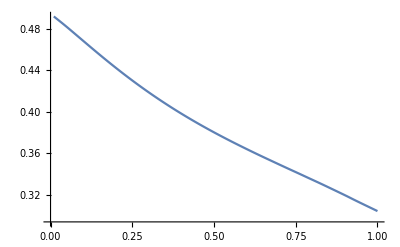

```mathematica
ListLinePlot[{datalin},InterpolationOrder->3]
```

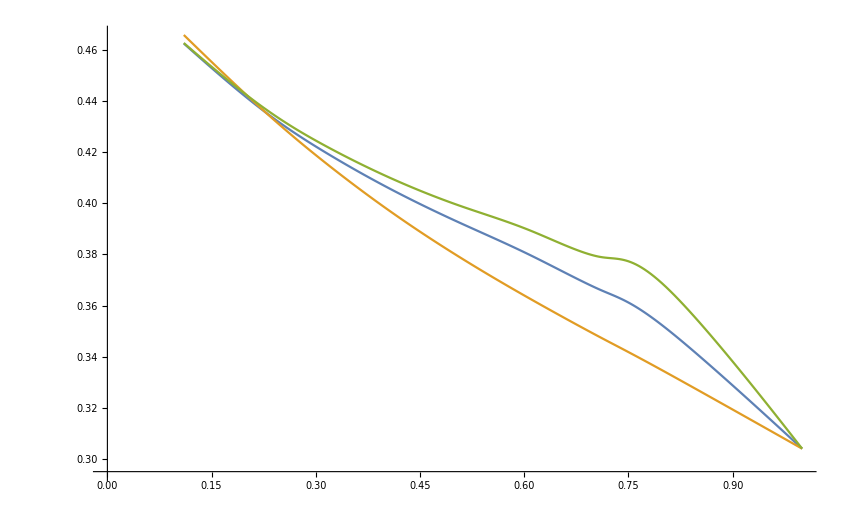

```mathematica
ListLinePlot[{datapower,datalin,datakink},InterpolationOrder->3]
```

```mathematica
avarpowersig[p0_]:=FinalSigma[wp[ρpower[0,p0]],Function[x,ρpower[x,p0]]][[2,2]]
avarlinsig[p0_]:=FinalSigma[wp[ρlinear[0,p0]],Function[x,ρlinear[x,p0]]][[2,2]]
avarkinksig[p0_]:=FinalSigma[wp[ρkink[0,p0]],Function[x,ρkink[x,p0]]][[2,2]]
datapowersig=Append[Table[{x,avarpowersig[x]},{x,0.01,.9,0.1}],{1,0.774}]
datalinsig=Append[Table[{x,avarlinsig[x]},{x,0.01,.9,0.1}],{1,0.774}]
```

{{0.01,0.961652},{0.11,0.990939},{0.21,1.00701},{0.31,1.01295},{0.41,1.0101},{0.51,0.998622},{0.61,0.977833},{0.71,0.946356},{0.81,0.90224},{1,0.774}}

{{0.01,0.959803},{0.11,0.969038},{0.21,0.965227},{0.31,0.953849},{0.41,0.937626},{0.51,0.917877},{0.61,0.895124},{0.71,0.869382},{0.81,0.840358},{1,0.774}}

```mathematica
datakinksig=Append[Table[{x,avarkinksig[x]},{x,0.01,.89,0.05}],{1,0.774}]
```

{{0.01,0.96166},{0.06,0.978569},{0.11,0.992169},{0.16,1.00316},{0.21,1.01203},{0.26,1.01909},{0.31,1.02454},{0.36,1.02849},{0.41,1.03095},{0.46,1.03185},{0.51,1.03101},{0.56,1.02819},{0.61,1.02303},{0.66,1.01501},{0.71,1.00362},{0.76,0.987822},{0.81,0.966847},{0.86,0.938835},{1,0.774}}

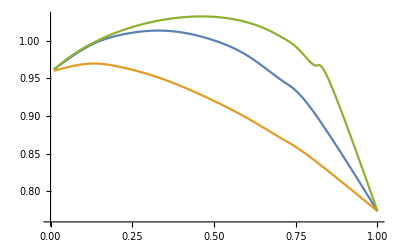

```mathematica
ListLinePlot[{datapowersig,datalinsig,datakinksig},InterpolationOrder->3]
```

```mathematica
avarkinksig[.76]
```

1.00924